```mathematica
kappa[c_][t_]:=Simplify[Cross[D[c[tt],tt],D[c[tt],{tt,2}]].Cross[D[c[tt],tt],D[c[tt],{tt,2}]]]^(1/2)/Simplify[D[c[tt],tt].D[c[tt],tt]]^(3/2)/.tt->t
tau[c_][t_]:=Simplify[Det[{D[c[tt],tt],D[c[tt],{tt,2}],D[c[tt],{tt,3}]}]]/Simplify[Cross[D[c[tt],tt],D[c[tt],{tt,2}]].Cross[D[c[tt],tt],D[c[tt],{tt,2}]]]/.tt->t
tang[c_][t_]:=D[c[tt],tt]/Simplify[D[c[tt],tt].D[c[tt],tt]]^(1/2)/.tt->t
nor[c_][t_]:=Simplify[Cross[binor[c][t],tang[c][t]]]
binor[c_][t_]:=Simplify[Cross[D[c[tt],tt],D[c[tt],{tt,2}]]]/Simplify[Factor[Cross[D[c[tt],tt],D[c[tt],{tt,2}]].Cross[D[c[tt],tt],D[c[tt],{tt,2}]]]]^(1/2)/.tt->t
```

```mathematica
c[t_] := {t*Cos[t],t*Sin[t],t}
kappa[c]
```

kappa[c]

```mathematica
FullSimplify[kappa[c]]
```

```mathematica
kappa[c][0]
```

1

```mathematica
tang[c][3]
```

{(Cos[3]-3 Sin[3])/(√11),(3 Cos[3]+Sin[3])/(√11),1/(√11)}

```mathematica
Simplify[c_'[0]/(√(c_'[0].c_'[0]))]
```

c_'[0]/(√(c_'[0].c_'[0]))

```mathematica
helix[a_,b_][t_]:={a*Cos[t],a*Sin[t],b*t}
```

```mathematica
p1=ParametricPlot3D[helix[2,1][t], {t,0,6*Pi}]
p2=ParametricPlot3D[helix[-1/2,1][t], {t,0,6*Pi}]
Show[p1,p2]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
tang[ellipse][2]
```

{-(2 Sin[2])/(√(Cos[2]^2+4 Sin[2]^2)),Cos[2]/(√(Cos[2]^2+4 Sin[2]^2))}

```mathematica
norplane[c_][t_] := {-tang[c][t][[2]],tang[c][t][[1]]}
norplane[ellipse][2];
```

```mathematica
{-Cos[2]/(√(Cos[2]^2+4 Sin[2]^2)),-(2 Sin[2])/(√(Cos[2]^2+4 Sin[2]^2))}

        tangprime[c_][t_] := D[tang[c][tt],tt]/.tt->t
kappaplane[c_][t_] := tangprime[c][t].norplane[c][t]
```

{-Cos[2]/(√(Cos[2]^2+4 Sin[2]^2)),-(2 Sin[2])/(√(Cos[2]^2+4 Sin[2]^2))}

```mathematica
1.584790,{t,0,2*Pi}]
```

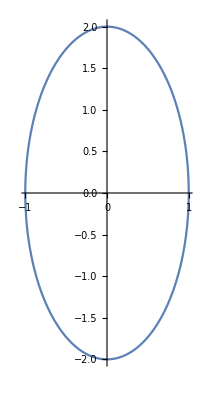

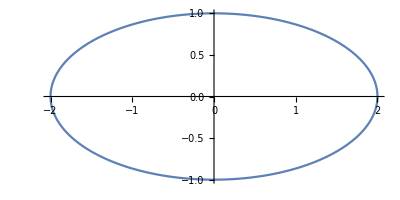

```mathematica
ellipse[t_] := {Cos[t],2*Sin[t]}
p1 = ParametricPlot[ellipse[t],{t,0,2*Pi}]
```

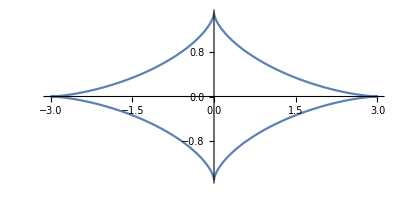

```mathematica
evolute[c_][t_]:= Simplify[c[t] + (D[c[tt],tt].D[c[tt],tt]) / (D[c[tt],{tt,2}].{-D[c[tt],tt][[2]],D[c[tt],tt][[1]]}) * {-D[c[tt],tt][[2]],D[c[tt],tt][[1]]}]/.tt->t
p2 = ParametricPlot[evolute[ellipse][t],{t,0,2*Pi}]
```

```mathematica
Show[p1,p2]
```

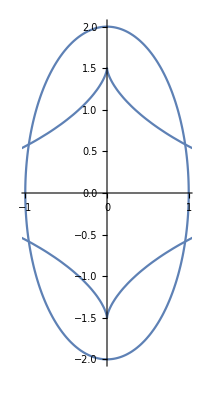

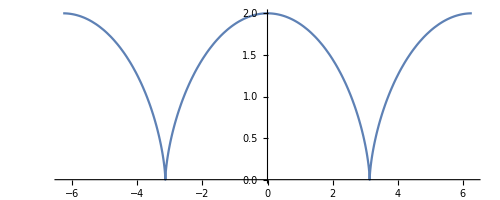

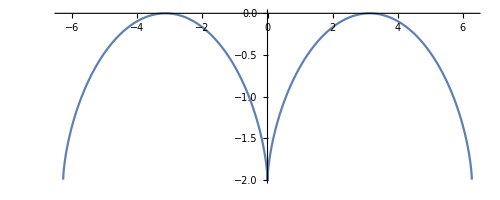

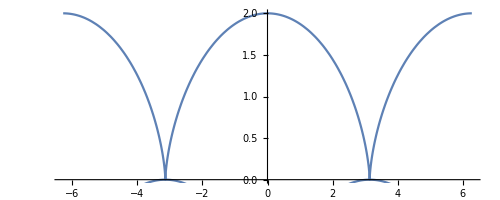

```mathematica
cycloid[t_] := {t+Sin[t],1+Cos[t]}
p1 = ParametricPlot[cycloid[t],{t,-2*Pi,2*Pi}]
p2 = ParametricPlot[evolute[cycloid][t],{t,-2*Pi,2*Pi}]
Show[p1,p2]
```

```mathematica
c = helix[1,2]
p1 = ParametricPlot3D[c[t],{t,-Pi,Pi}];
p2 = ParametricPlot3D[c[0] + t*tang[c][0] + kappa[c][0]*t^2/2*nor[c][0],{t,-Pi,Pi}];
p3 = ParametricPlot3D[c[0] + kappa[c][0]*t^2/2*nor[c][0] + kappa[c][0]*tau[c][0]*t^3/6*binor[c][0],{t,-Pi,Pi}];p4 = ParametricPlot3D[c[0] + t*tang[c][0]  + kappa[c][0]*tau[c][0]*t^3/6*binor[c][0],{t,-Pi,Pi}];
Show[p1,p2,p3,p4]
```

helix[1,2]

-Graphics3D-

```mathematica
ParametricPlot3D[{4*Cos[2*t]+2*Cos[t],4*Sin[2*t]-2*Sin[t],Sin[3*t]},{t,0,2*Pi}]
```

-Graphics3D-

```mathematica
c[t_]:={4*Cos[2*t]+2*Cos[t],4*Sin[2*t]-2*Sin[t]}
ParametricPlot[c[t], {t,0,2*Pi}]
```

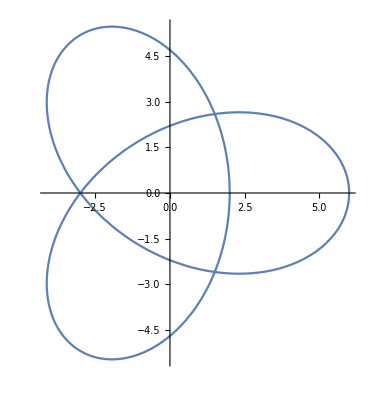
```mathematica
-Graphics-
Simplify[kappaplane[c][2]]
```

-Graphics-

(31-4 Cos[6])/(17-8 Cos[6])

```mathematica
Remove[torus];
torus[R_,r_][u_,v_]:={(R+r*Cos[u])*Cos[v],(R+r*Cos[u])*Sin[v],r*Sin[u]};
p1:=ParametricPlot3D[torus[3,1][u,v],{u,0,2*Pi},{v,0,2*Pi}]
p2:=ParametricPlot3D[torus[3,1][Pi*t,5*t],{t,0,30}]
Show[p1,p2]
```

-Graphics3D-